# Analyzing Economic Trends: A Comparative Study of Non-Linear Models,State-Space Models and Neural Networks

Muhammad Ali Hafeez

This computational essay explores the predictive accuracy of three models: non-linear model fits, state space models, and neural nets. The essay takes you on a journey from simple modeling techniques to discover the advantages of these techniques in a world where neural nets are gaining popularity. It is important to note that these modeling techniques are often used in conjunction with each other. However, for the purpose of comparing the models, they will be considered independently.

## Introduction

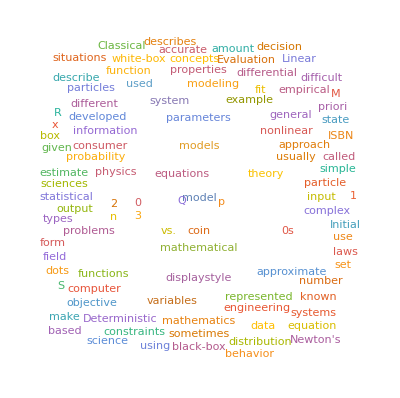

```mathematica
WordCloud[WikipediaData["Mathematical Modeling"]]
```

The purpose of this essay is to introduce a highly significant discussion. The emergence of machine learning has brought about groundbreaking advancements. However, have we thoroughly analyzed each technique in terms of their predictive power relative to one another? This essay aims to compare two crucial techniques: State-Space Models, specifically those employing the Kalman filter, and Neural Networks, which represent a more contemporary approach.

## Data

The data that will be used in this computational essay is the Federal Reserve of Economic Data (FRED) Real Gross Domestic Product data from 1947 to 2023.

```mathematica
data=Import["C:\\Users\\ali12\\Downloads\\GDP.xls"];
preprocessedData=data/. Null->"";
Dataset[preprocessedData]
```

```mathematica
gDPdataIcon=Iconize[preprocessedData,"GDPData"]
```

## Splitting the Data into Train and Test Sets

In this context, we will employ Mathematica to partition the dataset into separate testing and training sets. This division serves the purpose of evaluating the predictive capabilities of our models and safeguarding against the occurrence of overfitting.

```mathematica
whole=preprocessedData;
{trainer,tester}=ResourceFunction["TrainTestSplit"][(#1->#2)&@@#&/@Drop[#&@@whole,11],Shuffle->False];
Take[Dataset[trainer],10];
Take[Dataset[tester],10];
```

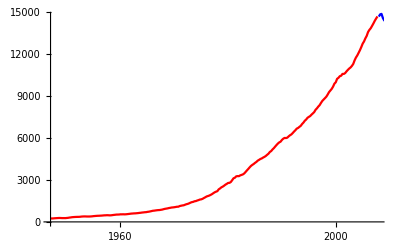

```mathematica
Show[ListLinePlot[TimeSeries[trainer],PlotStyle->Red],ListLinePlot[TimeSeries[tester],PlotStyle->Blue]]
```

## Adjustments to the Data (Relative Time)

```mathematica
InsertedvaluesTrain=Values[trainer];
InsertedvaluesTest=Values[tester];
InsertedkeysTrain=Range[0,0.25*(Length[InsertedvaluesTrain]-1),0.25];
InsertedkeysTest=Range[61,0.25*(Length[InsertedvaluesTest]-1)+61,0.25];
threadedValuesOfTrain=Thread[InsertedkeysTrain->InsertedvaluesTrain]
threadedValuesOfTest=Thread[InsertedkeysTest->InsertedvaluesTest];
Take[Dataset[threadedValuesOfTrain],10]
Take[Dataset[threadedValuesOfTest],10]
```

{0.→243.164,0.25→245.968,0.5→249.585,0.75→259.745,1.→265.742,1.25→272.567,1.5→279.196,1.75→280.366,2.→275.034,2.25→271.351,2.5→272.889,2.75→270.627,3.→280.828,3.25→290.383,3.5→308.153,3.75→319.945,4.→336.,4.25→344.09,4.5→351.385,4.75→356.178,5.→359.82,5.25→361.03,5.5→367.701,5.75→380.812,6.→387.98,6.25→391.749,6.5→391.171,6.75→385.97,7.→385.345,7.25→386.121,7.5→390.996,7.75→399.734,8.→413.073,8.25→421.532,8.5→430.221,8.75→437.092,9.→439.746,9.25→446.01,9.5→451.191,9.75→460.463,10.→469.779,10.25→472.025,10.5→479.49,10.75→474.864,11.→467.54,11.25→471.978,11.5→485.841,11.75→499.555,12.→510.33,12.25→522.653,12.5→525.034,12.75→528.6,13.→542.648,13.25→541.08,13.5→545.604,13.75→540.197,14.→545.018,14.25→555.545,14.5→567.664,14.75→580.612,15.→594.013,15.25→600.366,15.5→609.027,15.75→612.28,16.→621.672,16.25→629.752,16.5→644.444,16.75→653.938,17.→669.822,17.25→678.674,17.5→692.031,17.75→697.319,18.→717.79,18.25→730.191,18.5→749.323,18.75→771.857,19.→795.734,19.25→804.981,19.5→819.638,19.75→833.302,20.→844.17,20.25→848.983,20.5→865.233,20.75→881.439,21.→909.387,21.25→934.344,21.5→950.825,21.75→968.03,22.→993.337,22.25→1009.02,22.5→1029.96,22.75→1038.15,23.→1051.2,23.25→1067.38,23.5→1086.06,23.75→1088.61,24.→1135.16,24.25→1156.27,24.5→1177.68,24.75→1190.3,25.→1230.61,25.25→1266.37,25.5→1290.57,25.75→1328.9,26.→1377.49,26.25→1413.89,26.5→1433.84,26.75→1476.29,27.→1491.21,27.25→1530.06,27.5→1560.03,27.75→1599.68,28.→1616.12,28.25→1651.85,28.5→1709.82,28.75→1761.83,29.→1820.49,29.25→1852.33,29.5→1886.56,29.75→1934.27,30.→1988.65,30.25→2055.91,30.5→2118.47,30.75→2164.27,31.→2202.76,31.25→2331.63,31.5→2395.05,31.75→2476.95,32.→2526.61,32.25→2591.25,32.5→2667.57,32.75→2723.88,33.→2789.84,33.25→2797.35,33.5→2856.48,33.75→2985.56,34.→3124.21,34.25→3162.53,34.5→3260.61,34.75→3280.82,35.→3274.3,35.25→3331.97,35.5→3366.32,35.75→3402.56,36.→3473.41,36.25→3578.85,36.5→3689.18,36.75→3794.71,37.→3908.05,37.25→4009.6,37.5→4084.25,37.75→4148.55,38.→4230.17,38.25→4294.89,38.5→4386.77,38.75→4444.09,39.→4507.89,39.25→4545.34,39.5→4607.67,39.75→4657.63,40.→4722.16,40.25→4806.16,40.5→4884.56,40.75→5007.99,41.→5073.37,41.25→5190.04,41.5→5282.84,41.75→5399.51,42.→5511.25,42.25→5612.46,42.5→5695.37,42.75→5747.24,43.→5872.7,43.25→5960.03,43.5→6015.12,43.75→6004.73,44.→6035.18,44.25→6126.86,44.5→6205.94,44.75→6264.54,45.→6363.1,45.25→6470.76,45.5→6566.64,45.75→6680.8,46.→6729.46,46.25→6808.94,46.5→6882.1,46.75→7013.74,47.→7115.65,47.25→7246.93,47.5→7331.08,47.75→7455.29,48.→7522.29,48.25→7581.,48.5→7683.13,48.75→7772.59,49.→7868.47,49.25→8032.84,49.5→8131.41,49.75→8259.77,50.→8362.66,50.25→8518.83,50.5→8662.82,50.75→8765.91,51.→8866.48,51.25→8969.7,51.5→9121.1,51.75→9293.99,52.→9411.68,52.25→9526.21,52.5→9686.63,52.75→9900.17,53.→10002.2,53.25→10247.7,53.5→10318.2,53.75→10435.7,54.→10470.2,54.25→10599.,54.5→10598.,54.75→10660.5,55.→10783.5,55.25→10887.5,55.5→10984.,55.75→11061.4,56.→11174.1,56.25→11312.8,56.5→11566.7,56.75→11772.2,57.→11923.4,57.25→12112.8,57.5→12305.3,57.75→12527.2,58.→12767.3,58.25→12922.7,58.5→13142.6,58.75→13324.2,59.→13599.2,59.25→13753.4,59.5→13870.2,59.75→14039.6,60.→14215.7,60.25→14402.1,60.5→14564.1,60.75→14715.1}

## Using A Non-Linear Model

```mathematica
Clear[maxX];
Clear[minX];
AdjustedthreadedValuesOfTrain=Map[List@@#&,threadedValuesOfTrain];
AdjustedthreadedValuesOfTest=Map[List@@#&,threadedValuesOfTest];
Take[Dataset[AdjustedthreadedValuesOfTrain],10]
Take[Dataset[AdjustedthreadedValuesOfTest],10]
```

{{0.,243.164},{0.25,245.968},{0.5,249.585},{0.75,259.745},{1.,265.742},{1.25,272.567},{1.5,279.196},{1.75,280.366},{2.,275.034},{2.25,271.351},{2.5,272.889},{2.75,270.627},{3.,280.828},{3.25,290.383},{3.5,308.153},{3.75,319.945},{4.,336.},{4.25,344.09},{4.5,351.385},{4.75,356.178},{5.,359.82},{5.25,361.03},{5.5,367.701},{5.75,380.812},{6.,387.98},{6.25,391.749},{6.5,391.171},{6.75,385.97},{7.,385.345},{7.25,386.121},{7.5,390.996},{7.75,399.734},{8.,413.073},{8.25,421.532},{8.5,430.221},{8.75,437.092},{9.,439.746},{9.25,446.01},{9.5,451.191},{9.75,460.463},{10.,469.779},{10.25,472.025},{10.5,479.49},{10.75,474.864},{11.,467.54},{11.25,471.978},{11.5,485.841},{11.75,499.555},{12.,510.33},{12.25,522.653},{12.5,525.034},{12.75,528.6},{13.,542.648},{13.25,541.08},{13.5,545.604},{13.75,540.197},{14.,545.018},{14.25,555.545},{14.5,567.664},{14.75,580.612},{15.,594.013},{15.25,600.366},{15.5,609.027},{15.75,612.28},{16.,621.672},{16.25,629.752},{16.5,644.444},{16.75,653.938},{17.,669.822},{17.25,678.674},{17.5,692.031},{17.75,697.319},{18.,717.79},{18.25,730.191},{18.5,749.323},{18.75,771.857},{19.,795.734},{19.25,804.981},{19.5,819.638},{19.75,833.302},{20.,844.17},{20.25,848.983},{20.5,865.233},{20.75,881.439},{21.,909.387},{21.25,934.344},{21.5,950.825},{21.75,968.03},{22.,993.337},{22.25,1009.02},{22.5,1029.96},{22.75,1038.15},{23.,1051.2},{23.25,1067.38},{23.5,1086.06},{23.75,1088.61},{24.,1135.16},{24.25,1156.27},{24.5,1177.68},{24.75,1190.3},{25.,1230.61},{25.25,1266.37},{25.5,1290.57},{25.75,1328.9},{26.,1377.49},{26.25,1413.89},{26.5,1433.84},{26.75,1476.29},{27.,1491.21},{27.25,1530.06},{27.5,1560.03},{27.75,1599.68},{28.,1616.12},{28.25,1651.85},{28.5,1709.82},{28.75,1761.83},{29.,1820.49},{29.25,1852.33},{29.5,1886.56},{29.75,1934.27},{30.,1988.65},{30.25,2055.91},{30.5,2118.47},{30.75,2164.27},{31.,2202.76},{31.25,2331.63},{31.5,2395.05},{31.75,2476.95},{32.,2526.61},{32.25,2591.25},{32.5,2667.57},{32.75,2723.88},{33.,2789.84},{33.25,2797.35},{33.5,2856.48},{33.75,2985.56},{34.,3124.21},{34.25,3162.53},{34.5,3260.61},{34.75,3280.82},{35.,3274.3},{35.25,3331.97},{35.5,3366.32},{35.75,3402.56},{36.,3473.41},{36.25,3578.85},{36.5,3689.18},{36.75,3794.71},{37.,3908.05},{37.25,4009.6},{37.5,4084.25},{37.75,4148.55},{38.,4230.17},{38.25,4294.89},{38.5,4386.77},{38.75,4444.09},{39.,4507.89},{39.25,4545.34},{39.5,4607.67},{39.75,4657.63},{40.,4722.16},{40.25,4806.16},{40.5,4884.56},{40.75,5007.99},{41.,5073.37},{41.25,5190.04},{41.5,5282.84},{41.75,5399.51},{42.,5511.25},{42.25,5612.46},{42.5,5695.37},{42.75,5747.24},{43.,5872.7},{43.25,5960.03},{43.5,6015.12},{43.75,6004.73},{44.,6035.18},{44.25,6126.86},{44.5,6205.94},{44.75,6264.54},{45.,6363.1},{45.25,6470.76},{45.5,6566.64},{45.75,6680.8},{46.,6729.46},{46.25,6808.94},{46.5,6882.1},{46.75,7013.74},{47.,7115.65},{47.25,7246.93},{47.5,7331.08},{47.75,7455.29},{48.,7522.29},{48.25,7581.},{48.5,7683.13},{48.75,7772.59},{49.,7868.47},{49.25,8032.84},{49.5,8131.41},{49.75,8259.77},{50.,8362.66},{50.25,8518.83},{50.5,8662.82},{50.75,8765.91},{51.,8866.48},{51.25,8969.7},{51.5,9121.1},{51.75,9293.99},{52.,9411.68},{52.25,9526.21},{52.5,9686.63},{52.75,9900.17},{53.,10002.2},{53.25,10247.7},{53.5,10318.2},{53.75,10435.7},{54.,10470.2},{54.25,10599.},{54.5,10598.},{54.75,10660.5},{55.,10783.5},{55.25,10887.5},{55.5,10984.},{55.75,11061.4},{56.,11174.1},{56.25,11312.8},{56.5,11566.7},{56.75,11772.2},{57.,11923.4},{57.25,12112.8},{57.5,12305.3},{57.75,12527.2},{58.,12767.3},{58.25,12922.7},{58.5,13142.6},{58.75,13324.2},{59.,13599.2},{59.25,13753.4},{59.5,13870.2},{59.75,14039.6},{60.,14215.7},{60.25,14402.1},{60.5,14564.1},{60.75,14715.1}}

```mathematica
model=a x+b x^2+c x^3+d x^4+e;
nlm=NonlinearModelFit[AdjustedthreadedValuesOfTrain,model,{a,b,c,d,e},x]
```

FittedModel[328.004+2.21699 x-0.51451 x^2+0.0933 x^3-0.000370935 x^4]

```mathematica
equation=Normal[nlm]
```

328.004+2.21699 x-0.51451 x^2+0.0933 x^3-0.000370935 x^4

```mathematica
xValues=AdjustedthreadedValuesOfTest[[All,1]];
Dataset[xValues]
```

```mathematica
maxX=Max[xValues]
minX=Min[xValues]
```

76.

61.

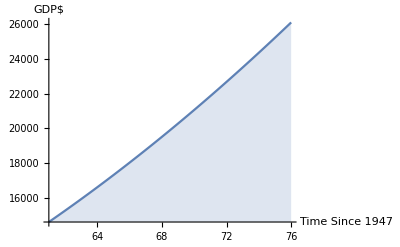

```mathematica
plotofmethod=Plot[nlm[x],{x,minX,maxX},Filling->Axis,AxesLabel->{"Time Since 1947","GDP$"}]
```

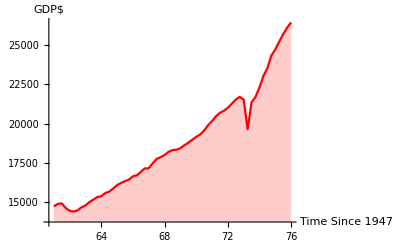

```mathematica
plotoftests=ListLinePlot[AdjustedthreadedValuesOfTest,PlotStyle->Red,Filling->Axis,AxesLabel->{"Time Since 1947","GDP$"}]
```

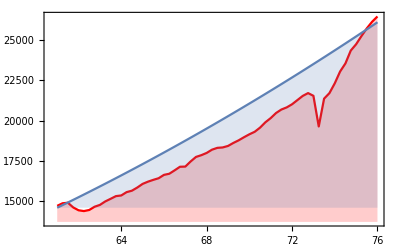
-Graphics-Gross Domestic Product ($)Time since 1947 (years)

```mathematica
Labeled[Show[plotoftests,plotofmethod,Frame->True,PlotStyle->Blue],{"Gross Domestic Product ($)","Time since 1947 (years)"},{Left,Top},RotateLabel->True]
```

## Using State Space Modeling

```mathematica
tsm=TimeSeriesModelFit[Values[threadedValuesOfTrain]]
```

TimeSeriesModel[…]

```mathematica
normaltsm=Normal[tsm]
```

SARIMAProcess[-159.593,{-0.413186},1,{0.60713,0.303489},{35,{},6,{}},505137.]

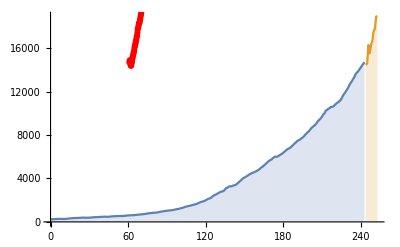
-Graphics-Gross Domestic Product ($)Time

```mathematica
Labeled[Show[ListLinePlot[{tsm["TemporalData"],TimeSeriesForecast[tsm,{10}]},Filling->Axis],ListPlot[output5,PlotStyle->Red]],{"Gross Domestic Product ($)","Time"},{Left,Top},RotateLabel->True
]
```

## Using Neural Networks

NetChain[<>]

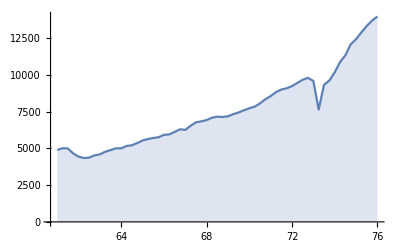
-Graphics-Gross Domestic Product ($)Error between the nueral net and test data

```mathematica
trainingData=Trainrules;
newKeyData=Keys[Testrules];
net=NetChain[{LinearLayer[10],Ramp,LinearLayer[1]}];
trainedNet=NetTrain[net,trainingData,LossFunction->MeanSquaredLossLayer[],Method->"ADAM",MaxTrainingRounds->10000,ValidationSet->Testrules]
testmodel={80,100,110,200};
trainedNet[testmodel];
NetPredictedValues=trainedNet[newKeyData];
graphicalrepnet=Thread[newKeyData->NetPredictedValues];
TestrulesNeccessaryState=Map[List,Testrules];
TestrulesNeccessaryalpha=Flatten[TestrulesNeccessaryState,1];
ErrorPresentedbetween=MapThread[#1[[1]]->(#1[[2]]-#2[[2]])&,{graphicalrepnet,TestrulesNeccessaryalpha}];
NegativeErrorPresentedbetween=Map[#1[[1]]->-#1[[2]]&,ErrorPresentedbetween];
Labeled[ListLinePlot[NegativeErrorPresentedbetween/. Rule->List,Filling->Axis],{"Gross Domestic Product ($)","Error between the nueral net and test data"},{Left,Top},RotateLabel->True
]
```

## Estimated Errors and their Implications

By a manual computation these are the estimated error areas of each model :

Non-linear model fit: The estimated area of the blue region is approximately 140,000 square units.

State Space Model: The estimated area between the red line and the blue line is approximately 2,300,000 square units.

Neural Net: The estimated area between the blue line and the x-axis is approximately 112,000 square units.

Based on the above results, we could conclude that on a limited amount of data a neural net would be the most appropriate simple model to use to make predictions on limited data.

## Limitations

Some limitations of the results include:

The existence of a limited amount of data may give rise to a circumstance wherein one method appears comparatively more appropriate than another.

The complexity of each algorithm may make one model better than the other and the complexity was not used as a quality indicator here.

Each model necessitated varying degrees of data cleaning; for instance, manipulating date objects in state space modeling was simpler, and the utilization of relative time was unnecessary.

It is worth noting that the simplicity of each model constituted a limitation to their predictive power.